```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["../Parameters"]

fy1=1;
fy2=2;
fy3=3;
fy4=4;

IntactPF=Import["../Intact/PartitionFunction_0_0.out","Table"];
IntactFE=Import["../Intact/FreeEnergy_0_0.out","Table"];
IntactdFE=Import["../Intact/dFreeEnergy_0_0.out","Table"];

FrayedPF1=Import["PartitionFunction_0_"<>ToString[fy1]<>".out","Table"];
FrayedFE1=Import["FreeEnergy_0_"<>ToString[fy1]<>".out","Table"];
FrayeddFE1=Import["dFreeEnergy_0_"<>ToString[fy1]<>".out","Table"];

FrayedPF2=Import["PartitionFunction_0_"<>ToString[fy2]<>".out","Table"];
FrayedFE2=Import["FreeEnergy_0_"<>ToString[fy2]<>".out","Table"];
FrayeddFE2=Import["dFreeEnergy_0_"<>ToString[fy2]<>".out","Table"];

FrayedPF3=Import["PartitionFunction_0_"<>ToString[fy3]<>".out","Table"];
FrayedFE3=Import["FreeEnergy_0_"<>ToString[fy3]<>".out","Table"];
FrayeddFE3=Import["dFreeEnergy_0_"<>ToString[fy3]<>".out","Table"];

FrayedPF4=Import["PartitionFunction_0_"<>ToString[fy4]<>".out","Table"];
FrayedFE4=Import["FreeEnergy_0_"<>ToString[fy4]<>".out","Table"];
FrayeddFE4=Import["dFreeEnergy_0_"<>ToString[fy4]<>".out","Table"];

fsTitle=24;
fsAxesLabel=18;
fs2=16;
```

/home/hemant/Desktop/code/dna/Nucleation_2/results/Frayed

{{},{L:,20.},{m:,40},{N:,5},{eta_b:,1.},{kappa_sigma_r:,1.},{Delta:,0.2469},{},{Extension Minimum:,0},{Extension Maximum:,25},{TOLERANCE:,0.}}

## Numerical Results

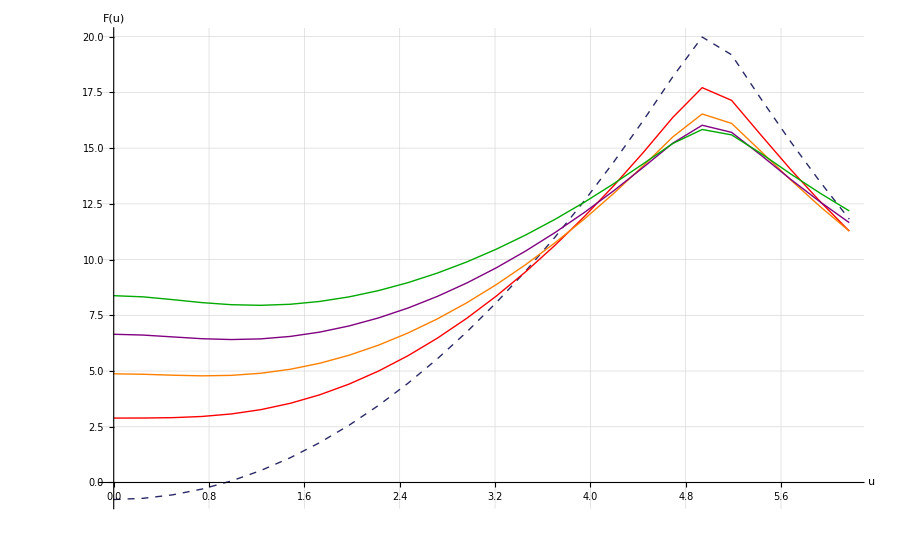

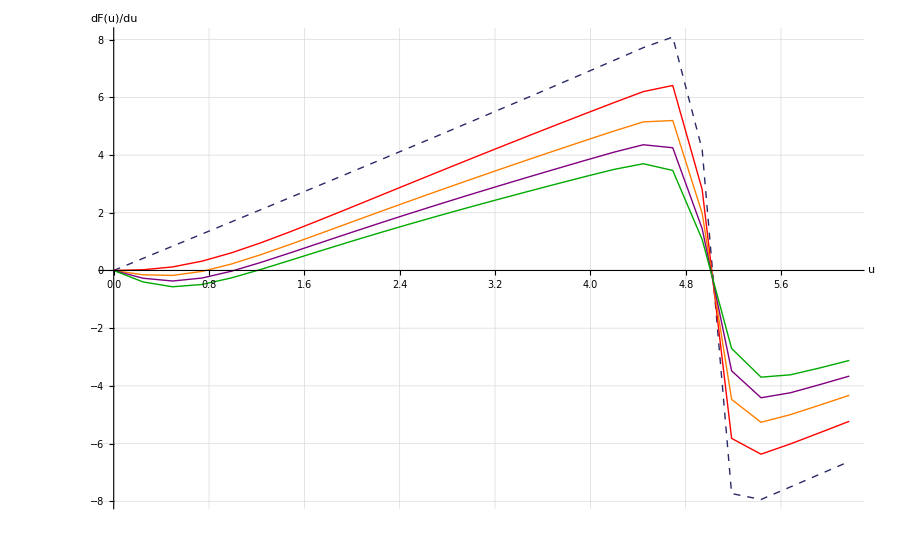

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

pIntactFE=ListLinePlot[IntactFE,PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]}];
pFrayedFE1=ListLinePlot[FrayedFE1,PlotStyle->{Thick,Red}];
pFrayedFE2=ListLinePlot[FrayedFE2,PlotStyle->{Thick,Orange}];
pFrayedFE3=ListLinePlot[FrayedFE3,PlotStyle->{Thick,Purple}];
pFrayedFE4=ListLinePlot[FrayedFE4,PlotStyle->{Thick,Darker[Green]}];

pdIntactdFE=ListLinePlot[IntactdFE,PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]}];
pdFrayedFE1=ListLinePlot[FrayeddFE1,PlotStyle->{Thick,Red}];
pdFrayedFE2=ListLinePlot[FrayeddFE2,PlotStyle->{Thick,Orange}];
pdFrayedFE3=ListLinePlot[FrayeddFE3,PlotStyle->{Thick,Purple}];
pdFrayedFE4=ListLinePlot[FrayeddFE4,PlotStyle->{Thick,Darker[Green]}];


legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],Line[{{0,0},{2,0}}]}],Style["Intact",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy1],FontSize->fs2]},{Graphics[{Thick,Orange,Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy2],FontSize->fs2]},{Graphics[{Thick,Purple,Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy3],FontSize->fs2]},{Graphics[{Thick,Darker[Green],Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy4],FontSize->fs2]}};

ShowLegend[Show[{pIntact,pFrayedFE1,pFrayedFE2,pFrayedFE3,pFrayedFE4},ImageSize->{900,600},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->{0.4,0.4},LegendPosition->{-0.8,0.05}}]

ShowLegend[Show[{pdIntact,pdFrayedFE1,pdFrayedFE2,pdFrayedFE3,pdFrayedFE4},ImageSize->{900,600},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF(u)/du",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->{0.4,0.4},LegendPosition->{-0.8,0.05}}]
```